## MKP pre 1D rovnicu vedenia tepla

Parametre ulohy

```mathematica
xL=0;xP=5;(*Hranice vypoctovej oblasti*)
a[x_]=(1+x);(*materialova charakteristika*)
f[x_]=x^2+10;(*prava strana*)
α1=0;β1=1;g1=1;(*Paramtre lavej OP*)
α2=1;β2=1;g2=1;(*Paramtre pravej OP*)
```

Presne riesenie

{{u[x]→1/18 (2791-186 x+3 x^2-2 x^3-168 Log[18]+168 Log[3 (1+x)])}}

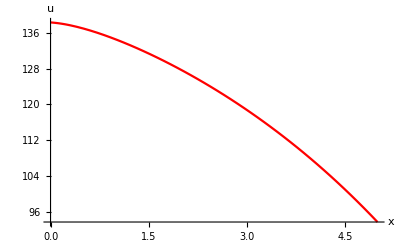

```mathematica
Rovnica=-D[a[x]u'[x],x]==f[x];
riesenie=DSolve[{
Rovnica,
α1 u[xL]+β1 (-a[xL]u'[xL])==g1,
α2 u[xP]+β2 (a[xP]u'[xP])==g2
},u[x],x]
uA[x_]=u[x]/.riesenie[[1]];
plotA=Plot[uA[x], {x,xL,xP},AxesLabel->{Style[x,Large],Style[u,Large]},PlotStyle->Red]
```

MKP, diskretizacia oblasti

```mathematica
s=2;(*stupen elementu*)
NN=2;(*Pocet elementov*)
n=NN*s+1;(*Celkovy pocet rovnic v globalnom systeme*)
H=(xP-xL)/NN;(*Velkost elementu (rovnomerne rozdelenie*)
He=H/s;(*Vzdialenost uzlovych bodov*)

xA[1]=xL;
xB[1]=H;
x[1,1]=xA[1]//N;
For[i=1,i≤s,i++,
x[1,i+1]=x[1,i]+He//N;
];
x[1,s+1]=xB[1]//N;(*nastavenie uzlov a premennych na okrajoch*)

For[i=2,i≤NN,i++,
xA[i]=xA[i-1]+H;
xB[i]=xB[i-1]+H;
x[i,1]=xA[i]//N;
    For[j=1,j≤s,j++,
         x[i,j+1]=x[i,j]+He//N;
        ];
x[i,s+1]=xB[i]//N;
](*nastavenie uzlov -zvysok*)
```

Inicializacia gausovych kvadratur

```mathematica
nk=Ceiling[1/2*Exponent[a[x],x]+2*s-1];
nf=Ceiling[1/2*Exponent[f[x],x]+s+1];
```

```mathematica
For[nn=1,nn≤10,nn++,
For[i=1,i≤nn,i++,
xi[nn,i]=x/.Solve[LegendreP[nn,x]==0,x][[i]]//N;
w[nn,i]=2/((1-xi[nn,i]^2)*(D[LegendreP[nn,x],x]/.x->xi[nn,i])^2);
]
]
GausQuad[nn_,f_,x_,a_,b_]:=(b-a)/2*∑_(i=1)^nn w[nn,i]*(f/.x->((b-a)/2 xi[nn,i]+(a+b)/2)) //N;
```

MKP, zostrojenie aproximacnych funkcii (Lagrangeov tvar)

```mathematica
For[i=1,i≤NN,i++,
For[j=1,j≤s+1,j++,
   ψ[i,j]=Product[If[j==k,1,(x-x[i,k])/(x[i,j]-x[i,k])],{k,1,s+1}];
    ];
]
```

MKP, zostrojenie lokalnych matic a pravych stran

```mathematica
For[e=1,e≤NN,e++,
K[e]=Table[GausQuad[nk,a[x]*D[ ψ[e,k],x]*D[ ψ[e,j],x],x,xA[e],xB[e]]//N,{j,1,s+1},{k,1,s+1}];
F[e]=Table[GausQuad[nf,f[x]* ψ[e,j],x,xA[e],xB[e]]//N,{j,1,s+1}];
];
```

MKP, zostrojenie globalnych matic a pravych stran

```mathematica
GlobK=Table[0,{n},{n}];(*Vytvorenie nulovej globalnej matice konecnoprvkovej sustavy rovnic*)
(*Pripocitavanie lokalnych matic tuhosti*)
```

```mathematica
GlobF=Table[0,{n}];(*Vytvorenie nulovej pravej strany konecnoprvkovej sustavy rovnic*)

(*Pripocitavanie lokalnych pravych stran*)
upCorner=1;
downCorner=s+1;(*nastavenie suradnic prvej lokalnej matice *)
For[i=1,i≤NN,i++,
GlobK[[upCorner;;downCorner,upCorner;;downCorner]]+=K[i];
GlobF[[upCorner;;downCorner]]+=F[i];

upCorner=downCorner;
downCorner=downCorner+s;(*posun na miesto pre dalsiu lokalnu maticu*)
]
```

```mathematica
GlobK//MatrixForm;
GlobF//MatrixForm;
```

MKP, zahrnutie okrajovych podmienok

```mathematica
(*Lavy okraj*)
If[β1==0,
GlobK[[1;;1,1;;n]]=0;
GlobK[[1,1]]=α1;
GlobF[[1]]=g1;(*Dirichletove okrajove podmienky*),
GlobK[[1,1]]+=α1/β1;GlobF[[1]]+=g1/β1;(*Neumannove a Newtonove podmienky*)
];

(*Pravy okraj*)
If[β2==0,
GlobK[[n;;n,1;;n]]=0;
GlobK[[n,n]]=α2;
GlobF[[n]]=g2;(*Dirichletove okrajove podmienky*),
GlobK[[n,n]]+=α2/β2;GlobF[[n]]+=g2/β2;(*Neumannove a Newtonove podmienky*)
];

GlobK//MatrixForm;
GlobF//MatrixForm;
```

MKP, riesenie rovnic, konstrukcia priblizneho riesenia, zobrazenie presneho aj priblizneho riesenia

```mathematica
(* riesenie systemu rovnic *)
solve=LinearSolve[GlobK,GlobF];
```

```mathematica
(* vykreslenie uzlovych neznamych *)
plotNpoints=ListPlot[Table[{xL+He*i,solve[[i+1]]},{i,0,n-1}],PlotStyle->{Blue}];
```

```mathematica
(* konstrukcia riesenia na elemente*)
For[i=1;k=1;,i≤NN,i++;,
  For[j=1;,j≤s,j++;k++,
    u[i,j]=solve[[k]];
    If[j==s,u[i,j+1]=solve[[k+1]]];
];
]

For[i=1,i≤NN,i++,
Ue[i]= ∑_(j=1)^(s+1) u[i,j]* ψ[i,j];
](*priblizne riesenia na elementoch*)
```

```mathematica
UNglob=Piecewise[Table[{Ue[i],xA[i]<x<xB[i]},{i,1,NN}]];(* konstrukcia celkoveho riesenia MKP*)
```

```mathematica
plotN=Plot[UNglob,{x,xL,xP}];
```

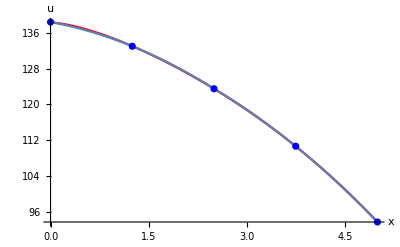

```mathematica
Show[plotA,plotN,plotNpoints]
```

MKP, vypocet EOC

```mathematica
L2Norm=Sqrt[NIntegrate[(uA[x]-UNglob)^2,{x,xL,xP}]];
ENorm=Sqrt[NIntegrate[a[x]*(D[uA[x],x]-D[UNglob,x])^2,{x,xL,xP}]];
LNS1={0.03768719713427668,0.009943063898282195,0.002530310062080743,0.0006358004824522421,0.00015916101282122892};
ENS1={0.11267228235829903,0.06076238163001318,0.030988429237351345,0.01557369073255096,0.007796925975296771};

LNS2={0.0014785256841187465,0.00021376586484195186,0.00002990557718034119,3.87588485661365*^-6,4.892068127397482*^-7};
ENS2={0.011442930032337924,0.0036549909824305166,0.0009942249782418145,0.0002546237766491915,0.00006405751127361775};

LNS3={0.0002960220185110387,0.000025857177553843186,1.8462723252744362*^-6,1.307860249655936*^-7,8.417727390779508*^-7};
ENS3={0.003365672345060595,0.0005516564495094414,0.00007644212760551788,9.857518015319393*^-6,2.9231818094470536*^-6};
EOCL2S1[1]="-";
EOCL2S2[1]="-";
EOCL2S3[1]="-";
EOCES1[1]="-";
EOCES2[1]="-";
EOCES3[1]="-";

For[i=2,i<5,i++,
EOCL2S1[i]=Log2[LNS1[[i-1]]/LNS1[[i]]]//N;
EOCL2S2[i]=Log2[LNS2[[i-1]]/LNS2[[i]]]//N;
EOCL2S3[i]=Log2[LNS3[[i-1]]/LNS3[[i]]]//N;
EOCES1[i]=Log2[ENS1[[i-1]]/ENS1[[i]]]//N;
EOCES2[i]=Log2[ENS2[[i-1]]/ENS2[[i]]]//N;
EOCES3[i]=Log2[ENS3[[i-1]]/ENS3[[i]]]//N;
]
(*s=1*)
aux=Table[{2^(i-1),LNS1[[i]],EOCL2S1[i],ENS1[[i]],EOCES1[i]},{i,1,4}];
Grid[{{"N(S1)","L2 CHYBA","EOC L2","Energ.chyba","EOC Energ."},aux[[1]],aux[[2]],aux[[3]],aux[[4]]},Frame->All]

(*s=2*)
aux=Table[{2^(i-1),LNS2[[i]],EOCL2S2[i],ENS2[[i]],EOCES2[i]},{i,1,4}];
Grid[{{"N(S2)","L2 CHYBA","EOC L2","Energ.chyba","EOC Energ."},aux[[1]],aux[[2]],aux[[3]],aux[[4]]},Frame->All]

(*s=3*)
aux=Table[{2^(i-1),LNS3[[i]],EOCL2S3[i],ENS3[[i]],EOCES3[i]},{i,1,4}];
Grid[{{"N(S3)","L2 CHYBA","EOC L2","Energ.chyba","EOC Energ."},aux[[1]],aux[[2]],aux[[3]],aux[[4]]},Frame->All]
```

N(S1) | L2 CHYBA | EOC L2 | Energ.chyba | EOC Energ.
1 | 0.0376872 | - | 0.112672 | -
2 | 0.00994306 | 1.92231 | 0.0607624 | 0.890882
4 | 0.00253031 | 1.97438 | 0.0309884 | 0.971449
8 | 0.0006358 | 1.99267 | 0.0155737 | 0.992619

N(S2) | L2 CHYBA | EOC L2 | Energ.chyba | EOC Energ.
1 | 0.00147853 | - | 0.0114429 | -
2 | 0.000213766 | 2.79006 | 0.00365499 | 1.64652
4 | 0.0000299056 | 2.83755 | 0.000994225 | 1.87822
8 | 3.87588×10^-6 | 2.94782 | 0.000254624 | 1.96521

N(S3) | L2 CHYBA | EOC L2 | Energ.chyba | EOC Energ.
1 | 0.000296022 | - | 0.00336567 | -
2 | 0.0000258572 | 3.51707 | 0.000551656 | 2.60905
4 | 1.84627×10^-6 | 3.80788 | 0.0000764421 | 2.85133
8 | 1.30786×10^-7 | 3.81934 | 9.85752×10^-6 | 2.95507